```mathematica
"There are Binomial[v,k]*2^k formulas length k with v possible variables, leading to a total of:";
∑_(k=0)^v Binomial[v,k]*2^k
```

3^v

```mathematica
"This means the number of bits required to represent an arbitrary formula is at least:";
Ceiling[Log2[3]*v]
```

Ceiling[(v Log[3])/Log[2]]

```mathematica
"This makes my representation, taking 2v bits per formula, is asymtotically this many times bigger:";
Limit[(2v)/Ceiling[(v Log[3])/Log[2]],v->∞]
N[%]
```

Log[4]/Log[3]

1.26186

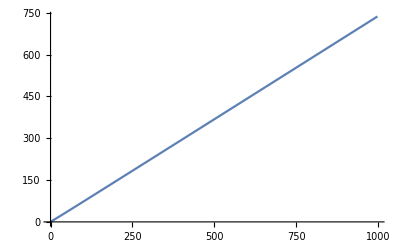

```mathematica
ListPlot[Table[√(-Log[(∑_(k=3)^n Binomial[n,k]*(k-1)!)/(3^Binomial[n,2])]),{n,3,1000}],Joined->True]
```

```mathematica
Table[∑_(k=3)^n Binomial[n,k]*(k-1)!,{n,3,10}]
```

{2,14,74,394,2344,16036,125628,1112028}